```mathematica
n =15;
m=(n-1)/2;
xInt[n_, j_]:=(2π j)/n
xval={};
Do[AppendTo[xval,xInt[n, j]],{j,0,n-1}]
```

```mathematica
xval
yval=Sin[x]^2/.x->xval
```

{0,(2 π)/15,(4 π)/15,(2 π)/5,(8 π)/15,(2 π)/3,(4 π)/5,(14 π)/15,(16 π)/15,(6 π)/5,(4 π)/3,(22 π)/15,(8 π)/5,(26 π)/15,(28 π)/15}

{0,Sin[(2 π)/15]^2,Cos[(7 π)/30]^2,5/8+(√5)/8,Cos[π/30]^2,3/4,5/8-(√5)/8,Sin[π/15]^2,Sin[π/15]^2,5/8-(√5)/8,3/4,Cos[π/30]^2,5/8+(√5)/8,Cos[(7 π)/30]^2,Sin[(2 π)/15]^2}

```mathematica
ak[m_,n_,k_]:=2/n∑_(j=1)^n yval[[j]]Cos[k*xval[[j]]];
bk[m_,n_,k_]:=2/n∑_(j=1)^n yval[[j]]Sin[k*xval[[j]]];
```

```mathematica
akval={};
bkval={};
Do[AppendTo[akval,ak[m,n,k]],{k,0,m}]
Do[AppendTo[bkval,bk[m,n,k]],{k,1,m}]
```

```mathematica
Pf[x_]:=akval[[1]]/2+∑_(k=2)^m (akval[[k]]Cos[(k-1) x]+bkval[[k-1]]Sin[(k-1) x])+akval[[-1]]/2 Cos[m x]
```

```mathematica
(*Graficando*)
```

```mathematica
data={};
Do[AppendTo[data,{xval[[i]],yval[[i]]}],{i,1,Length[xval]}]
```

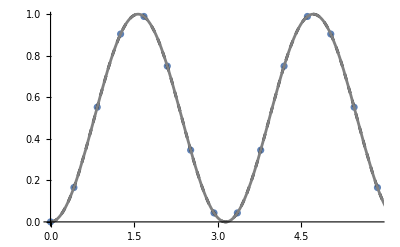

```mathematica
A=ListPlot[data];
B=Plot[Sin[x]^2,{x,0,2π},PlotStyle->{Dashed,Black}];
Cc=Plot[Pf[x],{x,0,2π},PlotStyle->Gray];
Show[{A,B,Cc}]
```

## Interpolacion impar

```mathematica
xval={0, 1,2,3,4}
yval=Sin[x]^2/.x->xval
```

{0,1,2,3,4}

{0,Sin[1]^2,Sin[2]^2,Sin[3]^2,Sin[4]^2}

```mathematica
Matriz={{1/2,Cos[x],Sin[x],Cos[2x],Sin[2x]}/.x->xval[[1]],
            {1/2,Cos[x],Sin[x],Cos[2x],Sin[2x]}/.x->xval[[2]],
  	 {1/2,Cos[x],Sin[x],Cos[2x],Sin[2x]}/.x->xval[[3]],
	   {1/2,Cos[x],Sin[x],Cos[2x],Sin[2x]}/.x->xval[[4]],
	   {1/2,Cos[x],Sin[x],Cos[2x],Sin[2x]}/.x->xval[[5]]};

MatrixForm[Matriz]
MatrixForm[{yval}]
```

(1/2 | 1 | 0 | 1 | 0
1/2 | Cos[1] | Sin[1] | Cos[2] | Sin[2]
1/2 | Cos[2] | Sin[2] | Cos[4] | Sin[4]
1/2 | Cos[3] | Sin[3] | Cos[6] | Sin[6]
1/2 | Cos[4] | Sin[4] | Cos[8] | Sin[8])

(0 | Sin[1]^2 | Sin[2]^2 | Sin[3]^2 | Sin[4]^2)

```mathematica
InvMatriz=Inverse[Matriz];
MatrixForm[InvMatriz]//Simplify
InvMatriz.yval//Simplify
```

(1/8 Csc[1/2]^2 Csc[1]^2 | -1/8 (-1+2 Cos[1]) Csc[1/2]^4 | 1/16 (1+Cos[1]+Cos[3]) Csc[1/2]^4 Sec[1/2]^2 | -1/8 (-1+2 Cos[1]) Csc[1/2]^4 | 1/8 Csc[1/2]^2 Csc[1]^2
((-1+2 Cos[1]-2 Cos[2]) Csc[1/2]^4)/(16+32 Cos[1]) | (Cos[1] (Cos[1]-Cos[2]+Cos[3]) Csc[1/2]^4)/(4+8 Cos[1]) | -1/8 (Cos[1]-Cos[2]+Cos[3]) Csc[1/2]^4 | (Cos[1] Cos[2] Csc[1/2]^4)/(4+8 Cos[1]) | -((-1+2 Cos[1]) Csc[1/2]^4)/(16+32 Cos[1])
-((1+2 Cos[1]+2 Cos[2]) Csc[1/2]^3 Sec[1/2])/(16+32 Cos[1]) | 1/8 (1+Cos[1]+Cos[3]) Csc[1/2]^3 Sec[1/2] | -1/8 (-1+2 Cos[1]) Csc[1/2]^4 Sin[2] | ((1+3 Cos[1]+2 Cos[2]+Cos[3]) Csc[1/2]^3 Sec[1/2])/(8+16 Cos[1]) | -1/8 Csc[1/2]^2 Csc[1]
((1-2 Cos[2]+2 Cos[4]) Csc[1/2]^4 Sec[1/2]^2)/(64 (1+2 Cos[1])) | ((-1+2 Cos[1]-2 Cos[2]+2 Cos[3]-2 Cos[4]) Csc[1/2]^4)/(16+32 Cos[1]) | 1/32 Cos[4] Csc[1/2]^4 Sec[1/2]^2 | -((-1+2 Cos[1]-2 Cos[2]+2 Cos[3]) Csc[1/2]^4)/(16+32 Cos[1]) | ((-1+2 Cos[2]) Csc[1/2]^4 Sec[1/2]^2)/(64 (1+2 Cos[1]))
((1+2 Cos[2]+2 Cos[4]) Csc[1/2]^2 Csc[2])/(8+16 Cos[1]) | -1/8 (1+2 Cos[3]) Csc[1/2]^2 Csc[1] | 1/8 Csc[1/2]^2 Csc[1]^2 Sin[4] | -((1+2 Cos[1]+2 Cos[2]+2 Cos[3]) Csc[1/2]^3 Sec[1/2])/(16+32 Cos[1]) | 1/8 Csc[1/2]^2 (Csc[1]-Csc[2]))

{1,0,0,-1/2,0}

```mathematica
P[x_]:= 1/2-Cos[2x]/2
```